```mathematica
n=5;
On[Assert];
(*Convert an index in our space to a one-hot set of occupied sites*)
iToS[i_]:=Block[{},Assert[1≤i≤2^n];PadLeft[IntegerDigits[i-1,2],n]];
(*Convert a bitset back to an index*)
sToI[s_]:=Block[{},Assert[AllTrue[s,#==0||#==1&]];1+FromDigits[s,2]];

(*Annihilation operator on a given site*)
a[site_]:=Block[{entries={}},
Do[
Block[{set=iToS[i]},
If[set[[site]]==1,
set[[site]]=0;
AppendTo[entries,{sToI[set],i}->
(-1)^(Total[set[[1;;site-1]]])]]],
{i,2^n}];
SparseArray[entries,{2^n,2^n}]
]

(*Creation operator on a given site*)
aD[site_]:=Block[{entries={}},
Do[
Block[{set=iToS[i]},
If[set[[site]]==0,
set[[site]]=1;
AppendTo[entries,{sToI[set],i}->
(-1)^(Total[set[[1;;site-1]]])]]],
{i,2^n}];
SparseArray[entries,{2^n,2^n}]
]
```

```mathematica
{a[1].a[2]==-a[2].a[1],
a[2].a[2]==SparseArray[{},{2^n,2^n}],
a[3].a[5]==-a[5].a[3],
a[3].a[4]!=-a[5].a[3],

aD[1].aD[2]==-aD[2].aD[1],
aD[2].aD[2]==SparseArray[{},{2^n,2^n}],
aD[3].aD[5]==-aD[5].aD[3],
aD[3].aD[4]!=-aD[5].aD[3],
aD[1].a[1]+a[1].aD[1]==IdentityMatrix[2^n],
Total[Sort[Eigenvalues[aD[3].a[3]]]]==2^(n-1),
Total[Sort[Eigenvalues[aD[1].a[1]]]]==2^(n-1)}
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
tFromRule[rule_]:=rule[[2]]aD[rule[[1,1]]].a[rule[[1,2]]];
uFromRule[rule_]:=rule[[2]]aD[rule[[1,1]]].aD[rule[[1,2]]].a[rule[[1,3]]].a[rule[[1,4]]]
```

```mathematica
Htu[t_,u_]:=Total[tFromRule/@(Most[ArrayRules[t]])]+Total[uFromRule/@(Most[ArrayRules[u]])]
```

```mathematica
test1[a_]:=Block[{H,T,U},
n=1;
H=N[Htu[{{a}},{}]];
Min[Eigenvalues[H]]
];
test2[a11_,a22_,a12_]:=Block[{H,T,U},
n=2;
T={{a11,a12},{a12,a22}};
H=N[Htu[T,{}]];
Min[Eigenvalues[H]]
];
testU[a11_,a22_,a12_,u_]:=Block[{H,T,U},
n=2;
T={{a11,a12},{a12,a22}};
U=SparseArray[{1,2,1,2}->u];
H=N[Htu[T,U]];
Min[Eigenvalues[H]]
];
testU3[w_,x_,y_,z_,u1212_,u1313_,u2323_,u1323_]:=Block[{T,U},
n=3;
T={{x,w,0},{w,y,0},{0,0,z}};
U=SparseArray[{
{1,2,1,2}->u1212,
{1,3,1,3}->u1313,
{2,3,2,3}->u2323,
{1,3,2,3}->u1323/2,
{2,3,1,3}->u1323/2
},{n,n,n,n}];
H=N[Htu[T,U]];
Min[Eigenvalues[H]]
];
testU3A[w1_,w2_,w3_,x_,y_,z_,u1212_,u1313_,u2323_,u1323_,u2123_]:=Block[{T,U},
n=3;
T={{x,w1,w2},{w1,y,w3},{w2,w3,z}};
U=SparseArray[{
{1,2,1,2}->u1212,
{1,3,1,3}->u1313,
{2,3,2,3}->u2323,
{1,3,2,3}->u1323/2,
{2,3,1,3}->u1323/2,
{2,1,2,3}->u2123/2,
{2,3,2,1}->u2123/2
},{n,n,n,n}];
H=N[Htu[T,U]];
Min[Eigenvalues[H]]
];
testU4A[w1_,w2_,w3_,w4_,w5_,w6_,v_,x_,y_,z_,u1212_,u1313_,u2323_,u2424_,u3434_,u1323_,u2123_,u1234_,u2124_,u1324_,u2423_]:=Block[{T,U},
n=4;
T={{v,w1,w2,w3},{w1,x,w4,w5},{w2,w4,y,w6},{w3,w5,w6,z}};
U=SparseArray[{
{1,2,1,2}->u1212,
{1,3,1,3}->u1313,
{2,3,2,3}->u2323,
{2,4,2,4}->u2424,
{3,4,3,4}->u3434,

{1,3,2,3}->0*u1323/2,
{2,3,1,3}->0*u1323/2,

{2,1,2,3}->0*u2123/2,
{2,3,2,1}->0*u2123/2,

{1,2,3,4}->0*u1234/2,
{3,4,1,2}->0*u1234/2,

{2,1,2,4}->0*u2124/2,
{2,4,2,1}->0*u2124/2,

{1,3,2,4}->0*u1324/2,
{2,4,1,3}->0*u1324/2,

{2,4,2,3}->0*u2423/2,
{2,3,2,4}->0*u2423/2
},{n,n,n,n}];
H=N[Htu[T,U]];
Min[Eigenvalues[H]]
];
```

```mathematica
{test1[-10]==-10.,
test1[+10]==0.0,
test2[-3,+4,0]==-3.0,
test2[+3,+4,0]==0.0,
test2[-3,-4,0]==-7.0,
test2[-3,-4,1]==-7.0,
Abs[test2[-3,-4,100000]-(-100003.5)]<1*^-5,
testU[0,0,0,1.0]==-1.0,
testU[-3,-4,0,1.0]==-8.0}

testU[-3,-4,0,-1.0]
testU[-3,0,-4,+1.0]
```

{True,True,True,True,True,True,True,True,True}

-6.

-5.772

```mathematica
(*1D Hubbard model. Compare with hubbard.jl*)
```

```mathematica
Hubbard1D[nSites_,hoppingT_,onsiteU_,periodic_,mu_]:=Block[{T,U,H,i2,e0},
n=2*nSites;
T=Array[0&,{n,n}];
U=SparseArray[{},{n,n,n,n}];
e0=0;
Do[
If[i+1<n||periodic,
i2=If[i+1<n,i+2,i+2-n];
T[[i,i2]]-=hoppingT;
T[[i2,i]]-=hoppingT;
]
,{i,n}];
Do[
T[[i,i]]-=mu;
,{i,n}];
Do[
i2=i+1;
U[[i,i2,i2,i]]+=onsiteU;
T[[i,i]]-=onsiteU/2;
T[[i2,i2]]-=onsiteU/2;
e0+=onsiteU/4;
,{i,1,n,2}];
H=N[Htu[T,U]];
H+e0 SparseArray[{{i_,i_}->offset},{2^n,2^n}]
];
```

```mathematica
HubbardE[nSites_,u_,mu_]:=Block[{},
offset=nSites*0.5+1.;
H=Hubbard1D[nSites,1,u,False,mu];
H-=SparseArray[{i_,i_}->offset,{2^n,2^n}];
Eigenvalues[H,1][[1]]+offset
(*Min[Eigenvalues[H]]+offset;*)
]
```

```mathematica
HubbardE[3,0.5]
```

-3.96733

```mathematica
Edata3=Table[{u,HubbardE[3,u]},{u,-2.7,2.7,0.3}]
```

{{-2.7,-4.525},{-2.4,-4.43549},{-2.1,-4.35387},{-1.8,-4.28019},{-1.5,-4.21445},{-1.2,-4.15657},{-0.9,-4.10641},{-0.6,-4.06376},{-0.3,-4.02839},{-4.44089×10^-16,-4.},{0.3,-3.97828},{0.6,-3.96288},{0.9,-3.95344},{1.2,-3.94962},{1.5,-3.95103},{1.8,-3.95735},{2.1,-3.96821},{2.4,-3.98329},{2.7,-4.0023}}

```mathematica
Edata4=Table[{u,HubbardE[4,u]},{u,-2.7,2.7,0.3}]
```

{{-2.7,-5.23596},{-2.4,-5.05548},{-2.1,-4.88365},{-1.8,-4.72123},{-1.5,-4.56907},{-1.2,-4.42809},{-0.9,-4.29938},{-0.6,-4.18416},{-0.3,-4.08383},{-4.44089×10^-16,-4.},{0.3,-4.08383},{0.6,-4.18416},{0.9,-4.29938},{1.2,-4.42809},{1.5,-4.56907},{1.8,-4.72123},{2.1,-4.88365},{2.4,-5.05548},{2.7,-5.23596}}

```mathematica
Edata5=Table[{u,HubbardE[5,u]},{u,-2.7,2.7,0.3}]
```

{{-2.7,-7.19223},{-2.4,-7.05133},{-2.1,-6.92606},{-1.8,-6.81639},{-1.5,-6.72217},{-1.2,-6.64314},{-0.9,-6.57899},{-0.6,-6.52936},{-0.3,-6.49388},{-4.44089×10^-16,-6.47214},{0.3,-6.46374},{0.6,-6.4683},{0.9,-6.4854},{1.2,-6.51461},{1.5,-6.55552},{1.8,-6.60765},{2.1,-6.67055},{2.4,-6.74372},{2.7,-6.82665}}

```mathematica
Edata6={{-8.,-14.0481},{-6.8,-12.5725},{-5.6,-11.2099},{-4.4,-10.0165},{-3.2,-9.06406},{-2.7,-8.75336},{-2.4,-8.59289},{-2.1,-8.45205},{-2.,-8.40946},{-1.8,-8.33076},{-1.5,-8.22882},{-1.2,-8.14595},{-0.9,-8.08187},{-0.8,-8.06464},{-0.6,-8.03631},{-0.3,-8.00907},{0,-8.},{0.3,-8.00907},{0.4,-8.01612},{0.6,-8.03631},{0.9,-8.08187},{1.2,-8.14595},{1.5,-8.22882},{1.6,-8.26066},{1.8,-8.33076},{2.1,-8.45205},{2.4,-8.59289},{2.7,-8.75336},{2.8,-8.8112},{4.,-9.66871},{5.2,-10.7899},{6.4,-12.1034},{7.6,-13.5463}};
```

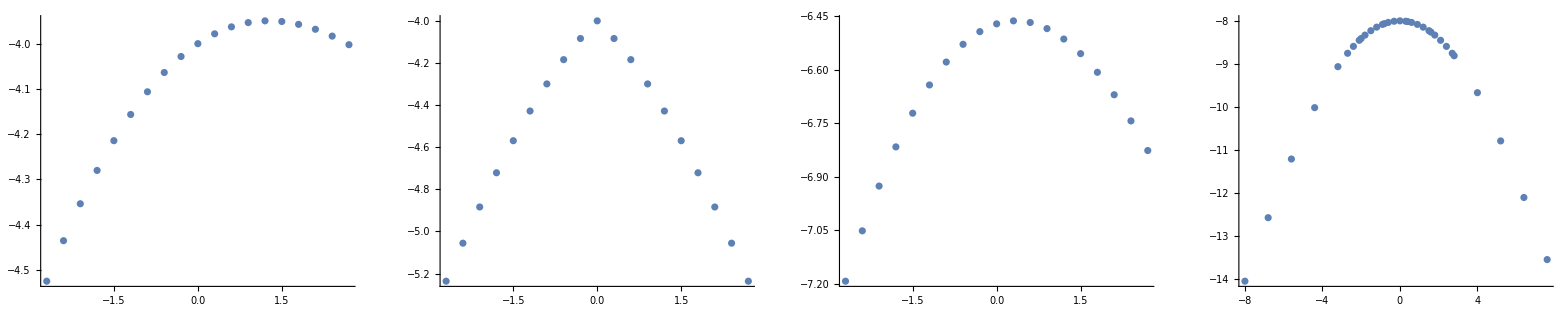

```mathematica
GraphicsGrid@List@(ListPlot/@{Edata3,Edata4,Edata5,Edata6})
```

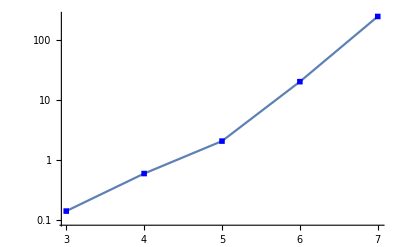

```mathematica
timesPerPoint={{3,0.1406},{4,0.5937},{5,2.0625},{6,20.187},{7,246.578}};
ListLogPlot[timesPerPoint,Joined->True,PlotMarkers->Style["■", Large, Blue]]
```

```mathematica
HubbardE[3,0.3]//Timing
```

{0.140625,-3.97828}

```mathematica
HubbardE[4,0.3]//Timing
```

{0.59375,-4.08383}

```mathematica
HubbardE[5,0.3]//Timing
```

{2.0625,-6.46374}

```mathematica
HubbardE[6,0.3]//Timing
```

{20.1875,-8.00907}

```mathematica
HubbardE[7,0.3]//Timing
```

{246.578,-8.98705}

```mathematica
{xs,gHF3,gHF4,gHF5,gHF6,gHF7,gHF8}=Transpose[Import["./UCSB_G1/GMPS/hubbard1D_dumbTest.csv"]];
```

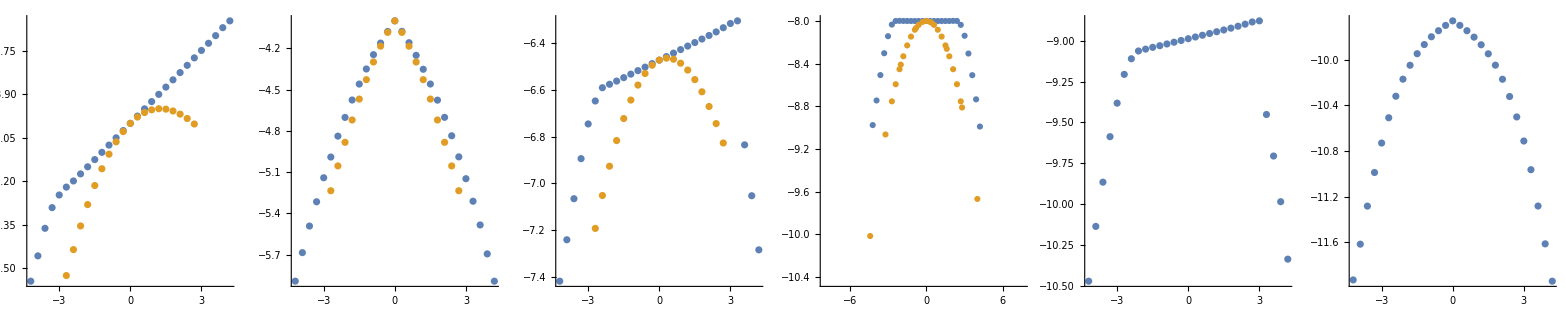

```mathematica
GraphicsGrid@(List@((
ListPlot[{Transpose[{xs,#2}],#1}]
&@@@{{Edata3,gHF3,3},{Edata4,gHF4,4},{Edata5,gHF5,5},{Edata6,gHF6,6}})~Join~{ListPlot[Transpose[{xs,gHF7}]],ListPlot[Transpose[{xs,gHF8}]]}))
```

```mathematica
Transpose[{xs,gHF4}][[9]]
```

{-1.8,-4.57601}

```mathematica
Edata4[[4]]
```

{-1.8,-4.72123}

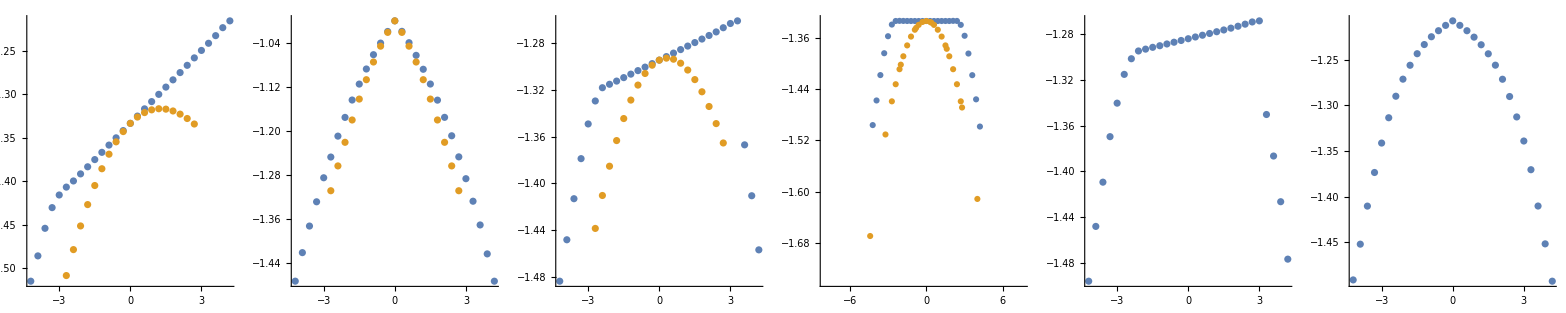

```mathematica
(*Normalized energy per site -- better for comparing different system sizes*)
GraphicsGrid@(List@((
ListPlot[{Transpose[{xs,#2/#3}],Transpose[{#1[[;;,1]],#1[[;;,2]]/#3}]}]
&@@@{{Edata3,gHF3,3},{Edata4,gHF4,4},{Edata5,gHF5,5},{Edata6,gHF6,6}})~Join~{ListPlot[Transpose[{xs,gHF7/7}]],ListPlot[Transpose[{xs,gHF8/8}]]}))
```

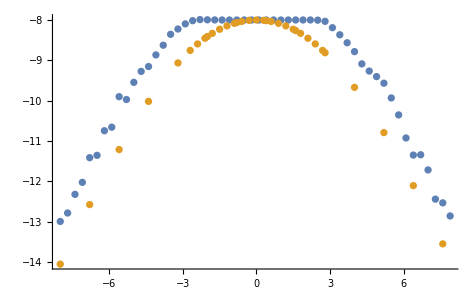

```mathematica
ListPlot[{Transpose@{xs,gHF},%200~Join~Edata5N}]
```

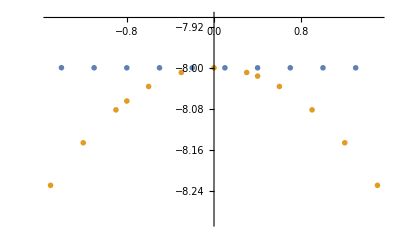

```mathematica
ListPlot[{Transpose@{xs,gHF},%200~Join~Edata5N},PlotRange->{{-1.5,1.5},{-8.3,-7.9}},MeshStyle->Directive[PointSize[10]],PlotMarkers->{Blue,Orange,Orange}]
```

```mathematica
Solve[aD+a==c2k&&-I(aD-a)==c2k1,{aD,a}]
```

{{aD→1/2 (c2k+ⅈ c2k1),a→1/2 (c2k-ⅈ c2k1)}}

```mathematica
1/4 (c2i**c2j+ⅈ c2i1**c2j+I c2i**c2j1-c2i1**c2j1)+
1/4 (c2i**c2j-ⅈ c2i1**c2j-I c2i**c2j1-c2i1**c2j1)//Expand
```

(c2i**c2j)/2-(c2i1**c2j1)/2

```mathematica
1/4 (c2i**c2j+ⅈ c2i1**c2j+I c2i**c2j1-c2i1**c2j1)-
1/4 (c2i**c2j-ⅈ c2i1**c2j-I c2i**c2j1-c2i1**c2j1)//Expand
```

(ⅈ c2i**c2j1)/2+(ⅈ c2i1**c2j)/2

```mathematica
1/4 (c2i**c2j-ⅈ c2i1**c2j+I c2i**c2j1+c2i1**c2j1)-
1/4 (c2i**c2j+I c2i1**c2j-I c2i**c2j1+c2i1**c2j1)//Expand
```

(ⅈ c2i**c2j1)/2-(ⅈ c2i1**c2j)/2

```mathematica
1/4 (c2i**c2j-ⅈ c2i1**c2j+I c2i**c2j1+c2i1**c2j1)+
1/4 (c2i**c2j+I c2i1**c2j-I c2i**c2j1+c2i1**c2j1)//Expand
```

(c2i**c2j)/2+(c2i1**c2j1)/2

```mathematica
{xs,HF05,gHF05}=Transpose[Import["./UCSB_G1/GMPS/hubbard1Dmu05.csv"]];
```

```mathematica
ListPlot[{Transpose[{xs,HF05}],Transpose[{xs,gHF05}],Edata4},PlotLegends->{HF,gHF,Exact},Joined->True,Mesh->All,MeshStyle->Directive[PointSize[Small],Black]]
```

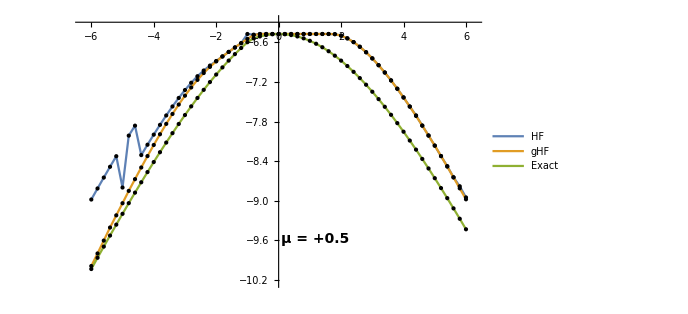

```mathematica
Transpose[{xs,HF05}]
```

{{-6.,-8.981},{-5.8,-8.81342},{-5.6,-9.31388},{-5.4,-8.48491},{-5.2,-8.96864},{-5.,-7.83358},{-4.8,-8.01244},{-4.6,-7.86156},{-4.4,-7.88284},{-4.2,-7.57202},{-4.,-7.99762},{-3.8,-7.84949},{-3.6,-7.70688},{-3.4,-7.57067},{-3.2,-7.44184},{-3.,-7.32165},{-2.8,-7.21131},{-2.6,-7.1123},{-2.4,-7.02598},{-2.2,-6.95217},{-2.,-6.88163},{-1.8,-6.81224},{-1.6,-6.74406},{-1.4,-6.67703},{-1.2,-6.61111},{-1.,-6.54626},{-0.8,-6.48243},{-0.6,-6.47214},{-0.4,-6.47214},{-0.2,-6.47214},{0.,-6.47214},{0.2,-6.47214},{0.4,-6.47214},{0.6,-6.47214},{0.8,-6.47214},{1.,-6.47214},{1.2,-6.47213},{1.4,-6.47213},{1.6,-6.47196},{1.8,-6.47464},{2.,-6.49703},{2.2,-6.53818},{2.4,-6.59516},{2.6,-6.66582},{2.8,-6.74854},{3.,-6.84199},{3.2,-6.94503},{3.4,-7.05662},{3.6,-7.1749},{3.8,-7.30197},{4.,-7.42292},{4.2,-7.56966},{4.4,-7.71133},{4.6,-7.85985},{4.8,-8.01086},{5.,-8.16487},{5.2,-8.32361},{5.4,-8.47644},{5.6,-8.62921},{5.8,-8.80172},{6.,-8.97907}}

```mathematica
Cases[Join@@{Transpose[{xs,HF05}],Transpose[{xs,gHF05}],Edata4},{-2.,_}]
```

{{-2.,-6.88162},{-2.,-6.88775},{-2.,-7.08715}}

```mathematica
Edata4=Table[{u,HubbardE[4,u,0.5]},{u,-6,6,0.2}]
```

{{-6.,-10.0343},{-5.8,-9.86373},{-5.6,-9.69466},{-5.4,-9.52725},{-5.2,-9.36161},{-5.,-9.19787},{-4.8,-9.03618},{-4.6,-8.87667},{-4.4,-8.7195},{-4.2,-8.56485},{-4.,-8.4129},{-3.8,-8.26383},{-3.6,-8.11785},{-3.4,-7.97516},{-3.2,-7.83598},{-3.,-7.70054},{-2.8,-7.56907},{-2.6,-7.44178},{-2.4,-7.31889},{-2.2,-7.20062},{-2.,-7.08715},{-1.8,-6.97867},{-1.6,-6.87529},{-1.4,-6.77714},{-1.2,-6.68428},{-1.,-6.59672},{-0.8,-6.53838},{-0.6,-6.50947},{-0.4,-6.48875},{-0.2,-6.47629},{0.,-6.47214},{0.2,-6.47629},{0.4,-6.48875},{0.6,-6.50947},{0.8,-6.53838},{1.,-6.57537},{1.2,-6.62031},{1.4,-6.67304},{1.6,-6.73338},{1.8,-6.80109},{2.,-6.87594},{2.2,-6.95767},{2.4,-7.04598},{2.6,-7.14058},{2.8,-7.24117},{3.,-7.34743},{3.2,-7.45905},{3.4,-7.57573},{3.6,-7.69717},{3.8,-7.82306},{4.,-7.95315},{4.2,-8.08714},{4.4,-8.2248},{4.6,-8.36588},{4.8,-8.51015},{5.,-8.65741},{5.2,-8.80745},{5.4,-8.96008},{5.6,-9.11515},{5.8,-9.27248},{6.,-9.43194}}

```mathematica
{xs,HF05,gHF05}=Transpose[Import["./UCSB_G1/GMPS/hubbard1Dmu05_20.csv"]];
```

```mathematica
ListPlot[{Transpose[{xs,HF05}],Transpose[{xs,gHF05}]},PlotLegends->{HF,gHF},Joined->True,Mesh->All,MeshStyle->Directive[PointSize[Small],Black]]
```

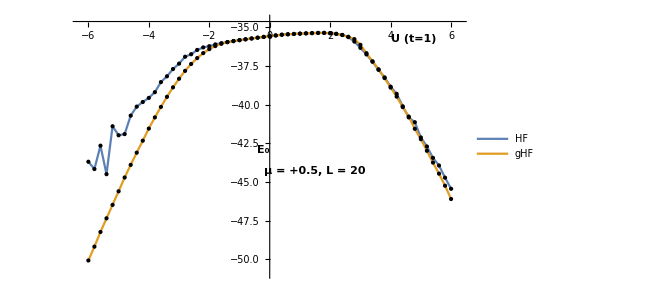

```mathematica
Edata6=Table[{u,HubbardE[6,u,0.5]},{u,-6,6,0.2}]
```

{{-6.,-15.1319},{-5.8,-14.8642},{-5.6,-14.5981},{-5.4,-14.334},{-5.2,-14.0718},{-5.,-13.8117},{-4.8,-13.5551},{-4.6,-13.3322},{-4.4,-13.1138},{-4.2,-12.9001},{-4.,-12.6915},{-3.8,-12.4884},{-3.6,-12.291},{-3.4,-12.0999},{-3.2,-11.9154},{-3.,-11.7378},{-2.8,-11.5676},{-2.6,-11.4052},{-2.4,-11.2508},{-2.2,-11.1049},{-2.,-10.9677},{-1.8,-10.8395},{-1.6,-10.7204},{-1.4,-10.6106},{-1.2,-10.5101},{-1.,-10.4189},{-0.8,-10.337},{-0.6,-10.2641},{-0.4,-10.2001},{-0.2,-10.1448},{0.,-10.0978},{0.2,-10.059},{0.4,-10.0592},{0.6,-10.0796},{0.8,-10.1079},{1.,-10.1442},{1.2,-10.1907},{1.4,-10.2635},{1.6,-10.3472},{1.8,-10.4415},{2.,-10.5463},{2.2,-10.6613},{2.4,-10.7861},{2.6,-10.9205},{2.8,-11.0639},{3.,-11.2161},{3.2,-11.3765},{3.4,-11.5448},{3.6,-11.7206},{3.8,-11.9033},{4.,-12.0926},{4.2,-12.288},{4.4,-12.4893},{4.6,-12.6959},{4.8,-12.9076},{5.,-13.124},{5.2,-13.3448},{5.4,-13.5698},{5.6,-13.7986},{5.8,-14.031},{6.,-14.2667}}

```mathematica
{xs,HF05,gHF05}=Transpose[Import["./UCSB_G1/GMPS/hubbard1Dmu05_6.csv"]];
```

```mathematica
ListPlot[{Transpose[{xs,HF05}],Transpose[{xs,gHF05}],Edata6},PlotLegends->{HF,gHF,Exact},Joined->True,Mesh->All,MeshStyle->Directive[PointSize[Small],Black]]
```

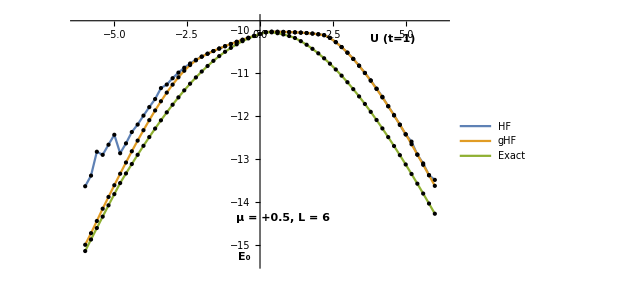

```mathematica
Edata4N=Table[{u,HubbardE[4,u,-0.5]},{u,-6,6,0.2}]
```

Eigenvalues::arh: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

{{-6.,-6.03435},{-5.8,-5.86373},{-5.6,-5.69466},{-5.4,-5.52725},{-5.2,-5.36161},{-5.,-5.19787},{-4.8,-5.03618},{-4.6,-4.87667},{-4.4,-4.7195},{-4.2,-4.56485},{-4.,-4.4129},{-3.8,-4.26383},{-3.6,-4.11785},{-3.4,-3.97516},{-3.2,-3.83598},{-3.,-3.70054},{-2.8,-3.56907},{-2.6,-3.44178},{-2.4,-3.31889},{-2.2,-3.20062},{-2.,-3.08715},{-1.8,-2.97867},{-1.6,-2.87529},{-1.4,-2.77714},{-1.2,-2.68428},{-1.,-2.59672},{-0.8,-2.53838},{-0.6,-2.50947},{-0.4,-2.48875},{-0.2,-2.47629},{0.,-2.47214},{0.2,-2.47629},{0.4,-2.48875},{0.6,-2.50947},{0.8,-2.53838},{1.,-2.57537},{1.2,-2.62031},{1.4,-2.67304},{1.6,-2.73338},{1.8,-2.80109},{2.,-2.87594},{2.2,-2.95767},{2.4,-3.04598},{2.6,-3.14058},{2.8,-3.24117},{3.,-3.34743},{3.2,-3.45905},{3.4,-3.57573},{3.6,-3.69717},{3.8,-3.82306},{4.,-3.95315},{4.2,-4.08714},{4.4,-4.2248},{4.6,-4.36588},{4.8,-4.51015},{5.,-4.65741},{5.2,-4.80745},{5.4,-4.96008},{5.6,-5.11515},{5.8,-5.27248},{6.,-5.43194}}

```mathematica
IsMono[a_]:=Ordering[Table[n+N[Sin[a n]],{n,1,100}]]==Range[100]
```

```mathematica
{xs,HF05,gHF05}=Transpose[Import["./UCSB_G1/GMPS/hubbard1DmuN05.csv"]];
```

```mathematica
ListPlot[{Transpose[{xs,HF05}],Transpose[{xs,gHF05}],Edata4N},PlotLegends->{HF,gHF,Exact},Joined->True,Mesh->All,MeshStyle->Directive[PointSize[Small],Black]]
```

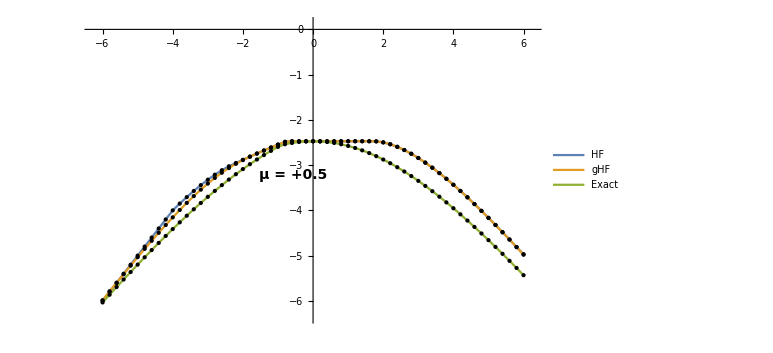

```mathematica
{xs,HF2D05,gHF2D05}=Transpose[Import["./UCSB_G1/GMPS/hubbard2D_12_12.csv"]];
```

```mathematica
ListPlot[{Transpose[{xs,HF2D05}],Transpose[{xs,gHF2D05}]},PlotLegends->{HF,gHF,Exact},Joined->True,Mesh->All,MeshStyle->Directive[PointSize[Small],Black]]
```

```mathematica
{xs,HF2D05,gHF2D05old}=Transpose[Import["./UCSB_G1/GMPS/hubbard2D_12_12.csv"]];
{xs,gHF2D05}=Transpose[Import["./UCSB_G1/GMPS/hubbard2D_12_12_better.csv"]];
```

```mathematica
ListPlot[{Transpose[{xs,HF2D05}],Transpose[{xs,gHF2D05}]},PlotLegends->{HF,gHF,Exact},Joined->True,Mesh->All,MeshStyle->Directive[PointSize[Small],Black]]
```

```mathematica
Product[{{k,1},{0,k}},{k,1,3}]
```

{{6,1},{0,6}}

```mathematica
state0:={1}~Join~(0 Range[2^n-1])
Dmat[psi_]:=Table[Conjugate[psi].aD[i].a[j].psi,{i,n},{j,n}]
DoubleOccOp[k_]:=aD[2k-1].a[2k-1].aD[2k].a[2k]
DoubleOcc[psi_]:=Table[Conjugate[psi].DoubleOccOp[i].psi,{i,1,n/2}]
EnergyAtT[psi_,T_]:=Conjugate[psi].Sum[T[[i,j]](aD[i].a[j]),{i,n},{j,n}].psi
```

```mathematica
n=4;SeedRandom[1234];

psi0=(0.23aD[4]+0.91aD[3]+0.95I aD[2]).(0.72 aD[1]+0.5aD[2]+0.43 aD[4]).state0;
psi0/=Norm[psi0]
Dmat[psi0]//MatrixForm
Eigenvalues[%]//Chop
DoubleOcc[psi0]//Chop
Det[Dmat[psi0][[1;;2,1;;2]]]//Chop
Det[Dmat[psi0][[3;;4,3;;4]]]//Chop

Tmat=RandomComplex[{-1-I,1+I},{n,n}];
(Tmat=(Tmat+ConjugateTranspose[Tmat])/2)//MatrixForm

EnergyAtT[psi0,Tmat]//Chop
Sum[Tmat[[i,j]]*Dmat[psi0][[i,j]],{i,n},{j,n}]//Chop

EnergyAtT[DoubleOccOp[2].psi0,Tmat*Table[Boole[i≤2&&j≤2],{i,n},{j,n}]]//Chop
Sum[(Tmat*Table[Boole[i≤2&&j≤2],{i,n},{j,n}])[[i,j]]*Det[Dmat[psi0][[{3,4,i},{3,4,j}]]],{i,n},{j,n}]//Chop

EnergyAtT[DoubleOccOp[2].psi0,Tmat]//Chop
Sum[Tmat[[i,j]]*
If[MemberQ[{2*2-1,2*2},i]||MemberQ[{2*2-1,2*2},j],
If[i==j,
Det[Dmat[psi0][[{3,4},{3,4}]]],
0],
Det[Dmat[psi0][[{i,3,4},{j,3,4}]]]
]
,{i,n},{j,n}]//Chop
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.323311+0. ⅈ,0.+0. ⅈ,-0.0950185+0.337522 ⅈ,-0.375943+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.136827+0. ⅈ,-0.541357+0. ⅈ,0.+0. ⅈ,0.-0.565153 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

(0.631188+0. ⅈ | 0.21652-0.046182 ⅈ | -0.0442375+0.212465 ⅈ | 0.365778+0.0537 ⅈ
0.21652+0.046182 ⅈ | 0.583681+0. ⅈ | -0.0307205-0.415074 ⅈ | 0.121546-0.077328 ⅈ
-0.0442375-0.212465 ⅈ | -0.0307205+0.415074 ⅈ | 0.53893+0. ⅈ | 0.109794-0.126889 ⅈ
0.365778-0.0537 ⅈ | 0.121546+0.077328 ⅈ | 0.109794+0.126889 ⅈ | 0.246201+0. ⅈ)

{1.,1.,0,0}

{0.319398,0.10453}

0.319398

0.10453

(0.753217+0. ⅈ | -0.466391+0.34103 ⅈ | -0.668427+0.585741 ⅈ | -0.16307+0.116681 ⅈ
-0.466391-0.34103 ⅈ | 0.854532+0. ⅈ | 0.303653+0.0634177 ⅈ | 0.364061+0.441867 ⅈ
-0.668427-0.585741 ⅈ | 0.303653-0.0634177 ⅈ | 0.969986+0. ⅈ | -0.199101-0.676264 ⅈ
-0.16307-0.116681 ⅈ | 0.364061-0.441867 ⅈ | -0.199101+0.676264 ⅈ | -0.472054+0. ⅈ)

0.864163

0.864163

0

0

0.0520488

0.0520488

```mathematica
psi0
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.323311+0. ⅈ,0.+0. ⅈ,-0.0950185+0.337522 ⅈ,-0.375943+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.136827+0. ⅈ,-0.541357+0. ⅈ,0.+0. ⅈ,0.-0.565153 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
DoubleOccOp[1].psi0
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.904889+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
DoubleOccOp[2].psi0
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0247035+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Dmat[psi0]
```

{{0.631188+0. ⅈ,0.21652-0.046182 ⅈ,-0.0442375+0.212465 ⅈ,0.365778+0.0537 ⅈ},{0.21652+0.046182 ⅈ,0.583681+0. ⅈ,-0.0307205-0.415074 ⅈ,0.121546-0.077328 ⅈ},{-0.0442375-0.212465 ⅈ,-0.0307205+0.415074 ⅈ,0.53893+0. ⅈ,0.109794-0.126889 ⅈ},{0.365778-0.0537 ⅈ,0.121546+0.077328 ⅈ,0.109794+0.126889 ⅈ,0.246201+0. ⅈ}}

```mathematica
Norm[psi0]
```

1.

```mathematica
Norm[(IdentityMatrix[2^n]+lam DoubleOccOp[1]).(IdentityMatrix[2^n]+lam DoubleOccOp[2]).psi0]^2//ComplexExpand//ExpandAll
```

1.+0.847856 lam+0.423928 lam^2

```mathematica
%/.{lam->10}
```

51.8714

```mathematica
%819/.{lam->-10}
```

34.9142

```mathematica
psi1=(IdentityMatrix[2^n]+lam DoubleOccOp[1]).(IdentityMatrix[2^n]+lam DoubleOccOp[2]).psi0//ExpandAll//Chop
```

{0,0,0,0.323311+0.323311 lam,0,-0.0950185+0.337522 ⅈ,-0.375943,0,0,-0.136827,-0.541357,0,(0.-0.565153 ⅈ)-(0.+0.565153 ⅈ) lam,0,0,0}

```mathematica
psi1N=Normalize[psi1]/.{lam->-0.3}
```

{0,0,0,0.255633,0,-0.107326+0.381242 ⅈ,-0.424639,0,0,-0.15455,-0.61148,0,0.-0.446851 ⅈ,0,0,0}

```mathematica
Conjugate[psi1N].(Sum[Tmat[[i,j]](aD[i].a[j]),{i,n},{j,n}]+U DoubleOccOp[1]+U DoubleOccOp[2]).psi1N/.{U->0.73}
```

0.978051+2.77556×10^-17 ⅈ